```mathematica
u[j_,m_,mp_,ω_,Θ_,Φ_]:=Block[{u=Cos[ω/2]-If[m+mp>=0,ⅈ,-ⅈ] Sin[ω/2]Cos[Θ],v=Sin[ω/2]Sin[Θ],maxs=If[m+mp>=0,Min[j-m,j-mp],Min[j+m,j+mp]]},(-ⅈ v)^(2j-Abs[m+mp])( u)^Abs[m+mp] Exp[-ⅈ (m-mp)Φ] Sqrt[(j+m)!(j-m)!(j+mp)!(j-mp)!]Sum[If[m+mp>=0,1/(s!(s+Abs[m+mp])!(j-m-s)!(j-mp-s)!),1/(s!(s+Abs[m+mp])!(j+m-s)!(j+mp-s)!)](1-v^-2)^s,{s,0,maxs}]]
```

```mathematica
SphericalHarmonicY[1,0,θ,ϕ]
```

1/2 √(3/π) Cos[θ]

```mathematica
SphericalHarmonicY[1,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
With[{l=0,m=0},Show[SphericalPlot3D[SphericalHarmonicY[l,m,θ,0],{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Red,Opacity[0.7],Specularity[White,10]],Mesh->None],SphericalPlot3D[-SphericalHarmonicY[l,m,θ,0],{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Blue,Opacity[0.7],Specularity[White,10]],Mesh->None],PlotRange->All,Boxed->False,Axes->False,Frame->False,Epilog->{Inset[Style["l="<>ToString[l]<>",m="<>ToString[m],40,Bold,Green],Scaled[{0.5,0.2}]]}]]
```

-Graphics3D-

```mathematica
tb[[4,1]]
```

-Graphics3D-

```mathematica
SphericalPlot3D[-SphericalHarmonicY[0,0,θ,0],{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
Grid[tb=Table[Show[SphericalPlot3D[Max[SphericalHarmonicY[l,m,θ,0],0],{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Red,Opacity[0.7],Specularity[White,10]],Mesh->None,PlotPoints->30],SphericalPlot3D[Max[-SphericalHarmonicY[l,m,θ,0],0],{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Blue,Opacity[0.7],Specularity[White,10]],Mesh->None,PlotPoints->30],PlotRange->All,Boxed->False,Axes->False,Frame->False,Epilog->{Inset[Style["l="<>ToString[l]<>",m="<>ToString[m],Italic,20,FontFamily->"Times"],Scaled[{0.5,0.2}],Background->White]}],{l,0,5},{m,0,l}]]
```

-Graphics3D- |  |  |  |  | 
-Graphics3D- | -Graphics3D- |  |  |  | 
-Graphics3D- | -Graphics3D- | -Graphics3D- |  |  | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |  | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

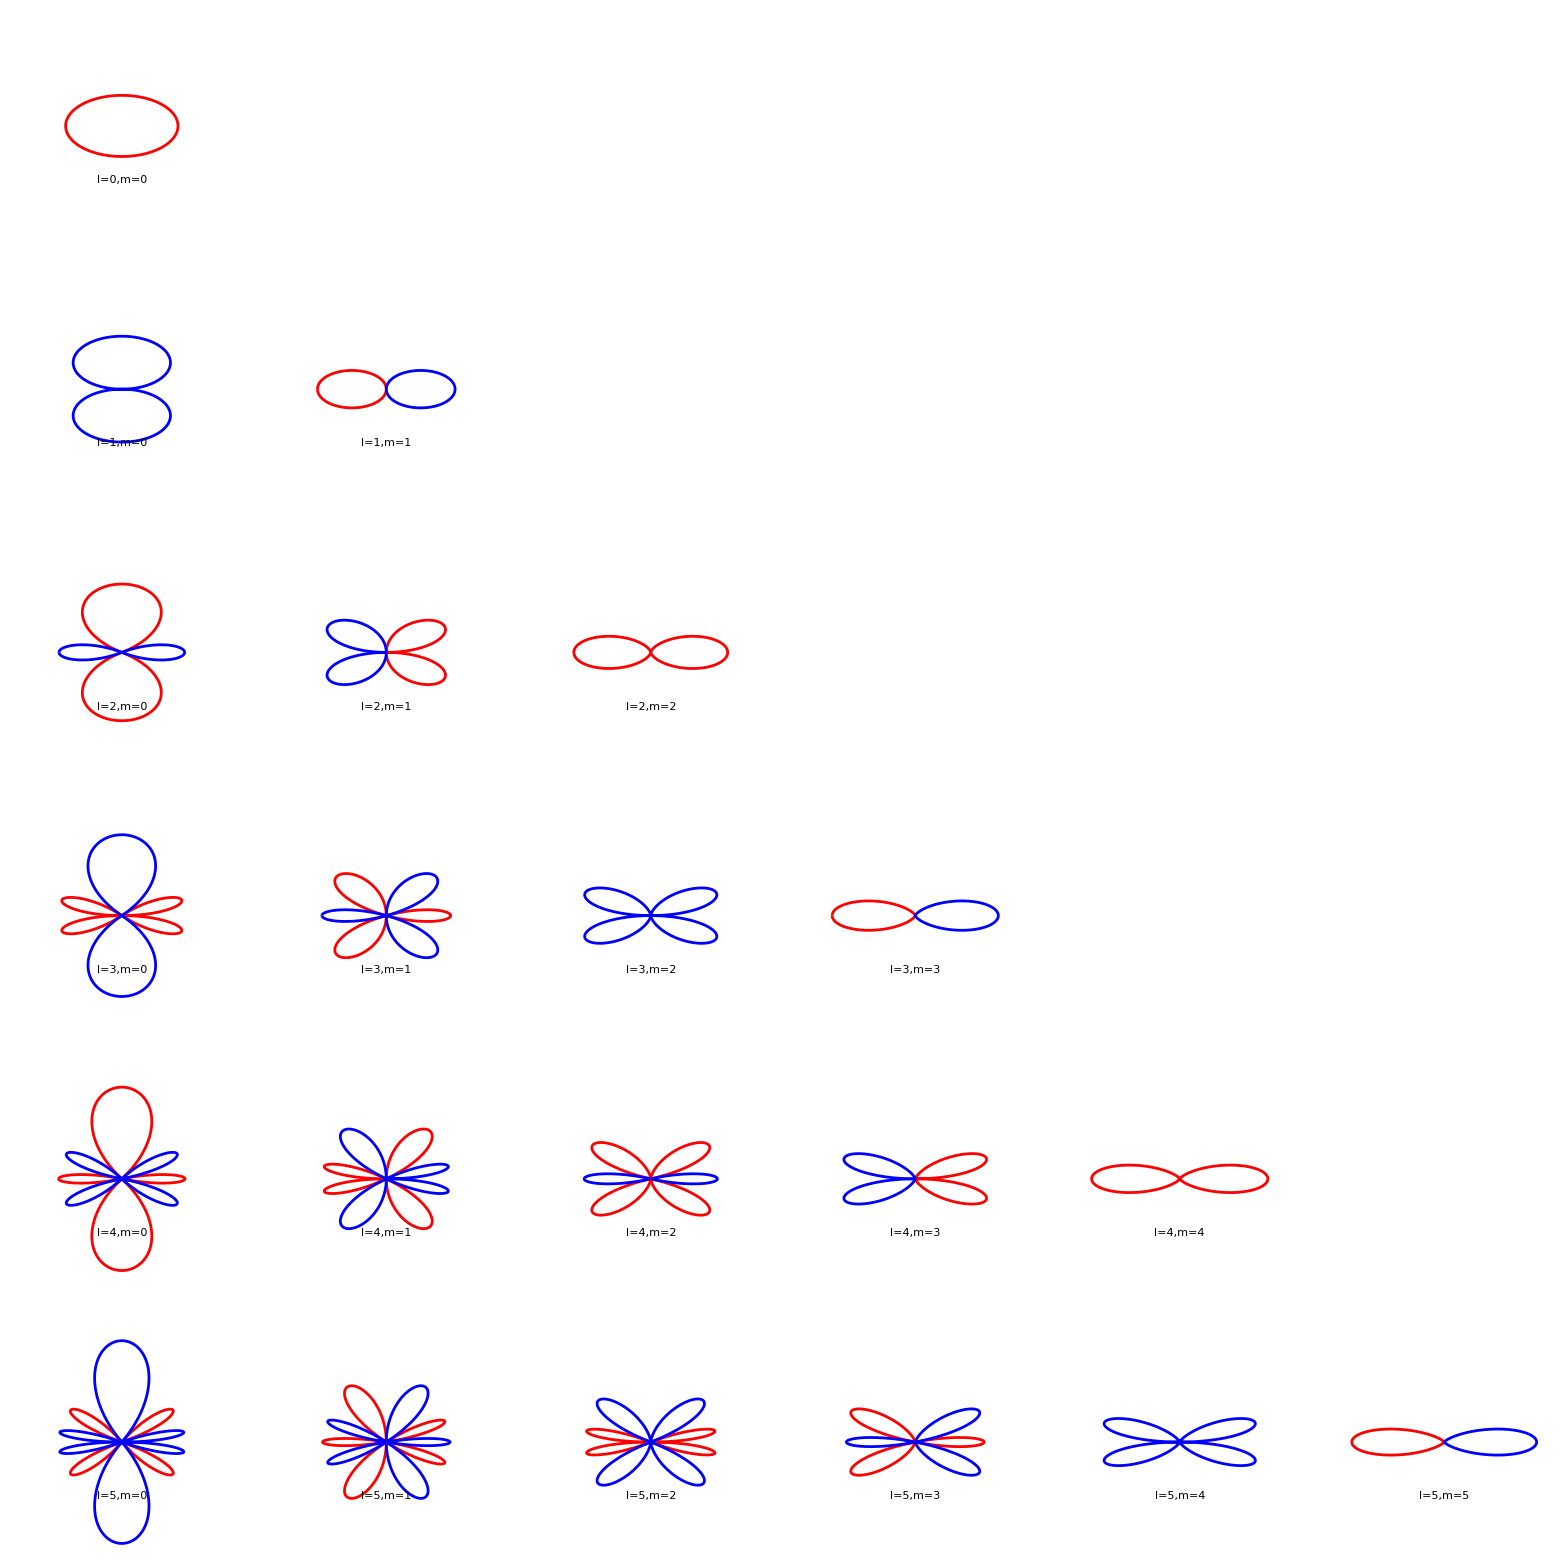

```mathematica
GraphicsGrid[Table[Show[{PolarPlot[Max[SphericalHarmonicY[l,m,Abs[θ]+π/2,0],0],{θ,-π,π},PlotStyle->Red],PolarPlot[Max[-SphericalHarmonicY[l,m,Abs[θ]+π/2,0],0],{θ,-π,π},PlotStyle->Blue],Graphics[Text["l="<>ToString[l]<>",m="<>ToString[m],{0,-0.5},Background->White]]},PlotRange->{{-0.5,0.5},{-0.95,0.95}},Axes->False],{l,0,5},{m,0,l}]]
```

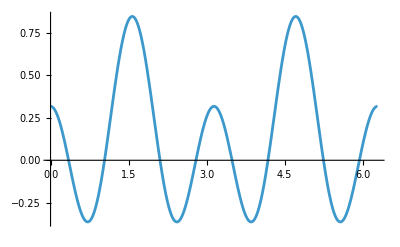

```mathematica
Plot[SphericalHarmonicY[4,0,θ+π/2,0],{θ,0,2π}]
```